```mathematica
n1=n2=1500;
```

```mathematica
Ax=Ay=0.02;
Au = Av=0.004;
f=0.25;
λ=700*10^(-9);
xmin=ymin=-Ax/2;
umin=vmin=-Au/2;
α=(-2π ⅈ)/(λ f);
```

```mathematica
(*produto dos A define a amplitude*)
```

```mathematica
(*Riscas*)
(*image = Table[If[ Mod[i,20]<10,2,0],{i,1,n1},{j,1,n1}];*)
(*Círculo*)
image = Table[If[ (i-n1/2-1)^2+(j-n1/2-1)^2<40^2&&Mod[j,10]<5,1,0],{i,1,n1},{j,1,n1}];
(*image = Table[If[ (i-n1/2-1)^2+(j-n1/2-1)^2<80^2 && Mod[i,10]<5,1,0],{i,1,n1},{j,1,n1}];
image = image+Table[If[ (i-n1/2-1)^2+(j-n1/2-1)^2<80^2 && Mod[j,10]<5,1,0],{i,1,n1},{j,1,n1}];*)
(*image = Table[If[ Abs[(i-n1/2-1)]<20&&Abs[(j-n1/2-1)]<20 && Mod[i,12]<5,1,0],{i,1,n1},{j,1,n1}];*)
(*image = Table[               If[j<-i+n1+100&&j>-i+n1-100&&i<j+300&&i>j-300  && Mod[i,12]<5,1,0],{i,1,n1},{j,1,n1}];
image =image+ Table[If[j<-i+n1+100&&j>-i+n1-100&&i<j+300&&i>j-300  && Mod[j,12]<5,1,0],{i,1,n1},{j,1,n1}];
image =image+ Table[If[i<j+100&&i>j-100&&j<-i+n1+300&&j>-i+n1-300  && Mod[i,12]<5,1,0],{i,1,n1},{j,1,n1}];
image =image+ Table[If[i<j+100&&i>j-100&&j<-i+n1+300&&j>-i+n1-300  && Mod[j,12]<5,1,0],{i,1,n1},{j,1,n1}];*)
(*Ponto*)
(*image = Table[If[ i==n1/2+1&&(j==740||j==760),1000,0],{i,1,n1},{j,1,n1}];*)
(*Imagem*)
(*image =ImageData[ColorSeparate[Import["/home/bernardo-silva/GoogleDrive/3_ano/2_semestre/lfea/OC/simulacao/AAriscas.png","Image"]][[1]]];
Dimensions[image]*)
Image[image,ImageSize->Medium]
```

-Graphics-

```mathematica
CorrectionIJ = Table[Exp[(-2π ⅈ)/(λ f)((i-1)/n1 Ax umin +(j-1)/n2 Ay vmin)],{i,1,n1},{j,1,n2}];
Dimensions[CorrectionIJ]
```

{1500,1500}

```mathematica
CorrectionKL= Table[Exp[α(umin xmin +vmin ymin)]Exp[(-2π ⅈ)/(λ f)((k-1)/n1 Au xmin +(l-1)/n2 Av ymin)],{k,1,n1},{l,1,n2}];
Dimensions[CorrectionKL]
```

{1500,1500}

```mathematica
fourier=CorrectionKL*Fourier[image*CorrectionIJ,FourierParameters->{1,(- Au Ax)/(λ f n1)}];
```

```mathematica
fourierABS = Abs[fourier]^2;
fourierABS=fourierABS/Max[fourierABS];
```

```mathematica
Image[10*fourierABS,ImageSize->Medium]
```

-Graphics-

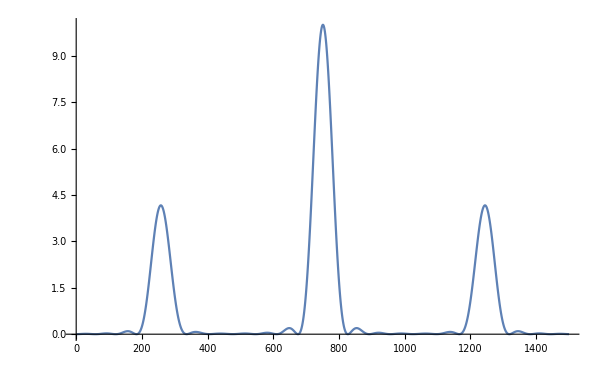

```mathematica
ListPlot[10*fourierABS[[n1/2+1,All]],Joined->True,PlotRange->All]
```

```mathematica
-Graphics-,-Graphics-,-Graphics-,-Graphics-;
```